```mathematica
ClearAll["Global`*"];
```

```mathematica
e=1.6 ×10^-19;
```

```mathematica
ϵo=8.85×10^-12;
```

```mathematica
Fq[r_]=(Z×e^2)/(4×π×ϵo×r^2);
Fq1[r_]=Fq[r×10^-13];
```

```mathematica
FqH[r_]=Fq1[r]/.Z->1;
FqC[r_]=Fq1[r]/.Z->6;
FqO[r_]=Fq1[r]/.Z->8;
```

```mathematica
rys1=Plot[FqH[r],{r,0.2,1},
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),
DisplayFunction->Identity];
rys2=Plot[FqC[r],{r,0.2,1},
PlotStyle->({{RGBColor[0,1,0], Thickness[0.006]}}),
DisplayFunction->Identity];
rys3=Plot[FqO[r],{r,0.2,1},
PlotStyle->({{RGBColor[0,0,1], Thickness[0.006]}}),
DisplayFunction->Identity];
```

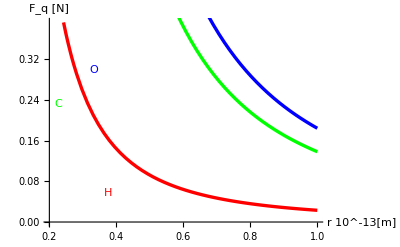

```mathematica
Show[rys1,rys2,rys3,DisplayFunction->$DisplayFunction,
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{"r  10^-13[m]","F_q [N] "},
Prolog->{Text[StyleForm["H",FontColor->RGBColor[1,0,0]],
Scaled[{0.23,0.16}]],
Text[StyleForm["C",FontColor->RGBColor[0,1,0]],
Scaled[{0.05,0.59}]],
Text[StyleForm["O",FontColor->RGBColor[0,0,1]],Scaled[{0.18,0.75}]]}]
```